# Mathematica Lab 2-Properties Fourier Transform Representation

## Property-Time reversal of a Discrete-Time Signal (with general explanations) *SCIMATH301 - Signals & Systems* *Joanikij Chulev* *10.11.2022*

```mathematica
x[n_]:=Sin[2n]/(π n) +(1/7)^n UnitStep[n];
(* This is Signal 1. *)
(* We are defining the signal itself here. *)
(* It is Non-Periodic. *)
(* This signal is defiened in the TIME domain! *)
```

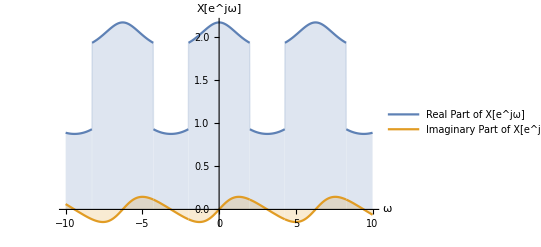

```mathematica
X[ω_]=FourierSequenceTransform[x[n],n,ω,FourierParameters->{1, -1}];
(* We are Fourier transforming the signal itself here. *)
(* It is Non-Periodic. *)
(* This signal is defiened in the FREQUENCY domain! *)

PX=Plot[{Re[X[ω]],Im[X[ω]]},{ω,-10,10},Filling->Axis,PlotRange->All,AxesLabel->{"ω","X[e^jω]"},PlotLegends->{"Real Part of X[e^jω]","Imaginary Part of X[e^jω]"}]
(* We Plot the Real and Imaginary parts of the signal function, see labels in graph plot. *)
```

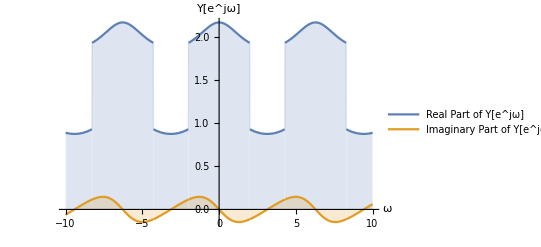

```mathematica
Y[ω_]:=X[-ω];
(* Here we use Table 5.1 to get the Fourier Transform of the time reversal, thus we apply the property. *)
(*  5.3.6 = Time Reversal =x(-n) thus X(e^-jw)  *)
(* We get a new signal which is the reversed version of the original singal. *)
PY=Plot[{Re[Y[ω]],Im[Y[ω]]},{ω,-10,10},Filling->Axis,PlotRange->All,AxesLabel->{"ω","Y[e^jω]"},PlotLegends->{"Real Part of Y[e^jω]","Imaginary Part of Y[e^jω]"}]
(* We Plot the Real and Imaginary parts of the signal function, see labels in graph plot. *)
```

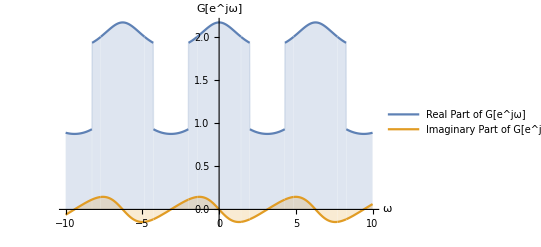

```mathematica
g[n] := x[-n];
(* Here we Time Reverse the signal in the time domain to get a new signal.  *)
(* x[-n]  *)
(* We get a new signal which is the reversed version of the original singal. *)
G[ω_]=FourierSequenceTransform[g[n],n,ω,FourierParameters->{1, -1}];
(* We are Fourier transforming the signal itself here so we can prove the property later on. *)
(* It is Non-Periodic. *)
(* This signal is defiened in the FREQUENCY domain! *)
PG=Plot[{Re[G[ω]],Im[G[ω]]},{ω,-10,10},Filling->Axis,PlotRange->All,AxesLabel->{"ω","G[e^jω]"},PlotLegends->{"Real Part of G[e^jω]","Imaginary Part of G[e^jω]"}]
(* We Plot the Real and Imaginary parts of the signal function, see labels in graph plot. *)
```

```mathematica
Simplify[G[ω]==Y[ω]]   (*We prove this is true with both approaches, thus we prove the proeprty*)
```

True

```mathematica
GraphicsGrid[{{PX, PY, PG}},Frame->True] (* Zoom out or scroll left to see all graphs. And we can compare G[ω] and Y[ω] visually and see they are the same, thus the property is TRUE. *)
```

-Graphics-